## Statistical mixtures from time averaging - ∞ square well

Define the stationary states:

```mathematica
Subscript[ψ, n_]:=x|->√(2/L)Piecewise[{{Sin[n π x/L], EvenQ[n]}, {Cos[n π x/L], OddQ[n]}}]
```

Add some assumptions about parameters/variables to make simplification easier later

```mathematica
assump=(x|ξ|t|τ)∈Reals&&(L|m|ℏ)∈PositiveReals
```

(x|ξ|t|τ)∈ℝ&&(L|m|ℏ)∈ℝ&&L>0&&m>0&&ℏ>0

```mathematica
Subscript[ℰ, n_]=(n^2 π^2 ℏ^2)/(2 m L^2);
Subscript[ω, n_]=Subscript[ℰ, n]/ℏ;
```

Plot a few stationary states. Notice they are either even or odd:

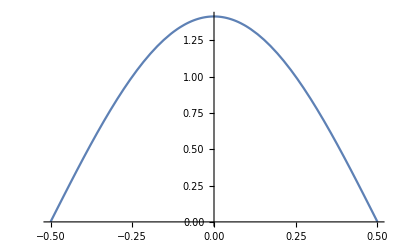
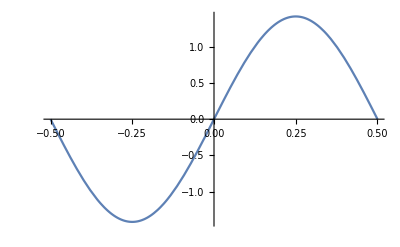
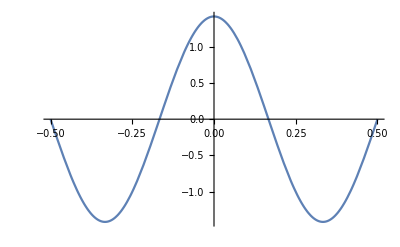
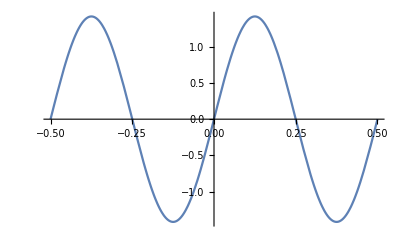
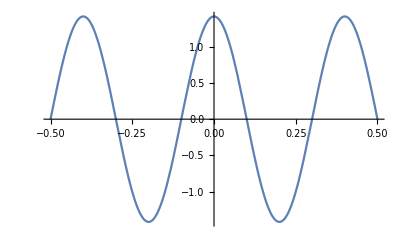

```mathematica
Table[Plot[√L Subscript[ψ, n][x/L]/.{L->1},{x,-1/2,1/2}],{n,1,5}]
```

Define a super-position for the initial state and add the phase evolutions for each stationary state

```mathematica
Ψ[x_,t_]=1/(√2)Subscript[ψ, 1][x] Exp[-I Subscript[ℰ, 1] t /ℏ]-1/(√2)Subscript[ψ, 2][x] Exp[-I Subscript[ℰ, 2] t /ℏ];
```

Un-comment run the following cell only if you want to experiment with random coefficients! (Note that it will re-define the variable Ψ, so make sure you either run the cell above (what we did in discussion) or the cell below (random coefficients for super-position)

```mathematica
(*Ψ[x_,t_]=∑_(n=1)^5 Subscript[c, n] Subscript[ψ, n][x] Exp[-I Subscript[ℰ, n] t /ℏ]/.Thread[Table[Subscript[c, n],{n,1,5}]->Normalize[{1,I}.#&/@RandomVariate[NormalDistribution[],{5,2}]]];*)
```

Symbolically compute the PDF () for Ψ, and choose dimensionless variables for plotting

```mathematica
ddPDF[ξ_,τ_]=ComplexExpand[L Abs[ Ψ[L ξ,(2π)/(3 Subscript[ω, 1]) τ]]^2]/.L->1;
```

Make an animation of the PDF. The particle ‘sloshes’ around:

```mathematica
Manipulate[Plot[ddPDF[ξ,τ],{ξ,-1/2,1/2},PlotRange->{-0.1,4},Ticks->{{{-1/2,-L/2},{1/2,L/2}},{1,2,3,4}},AxesLabel->{"",""},Epilog->{Style[Text[ToString[τ]<>" periods",{0.4,3.8}],FontSize->14]}],{τ,0,1}]
```

Make a table

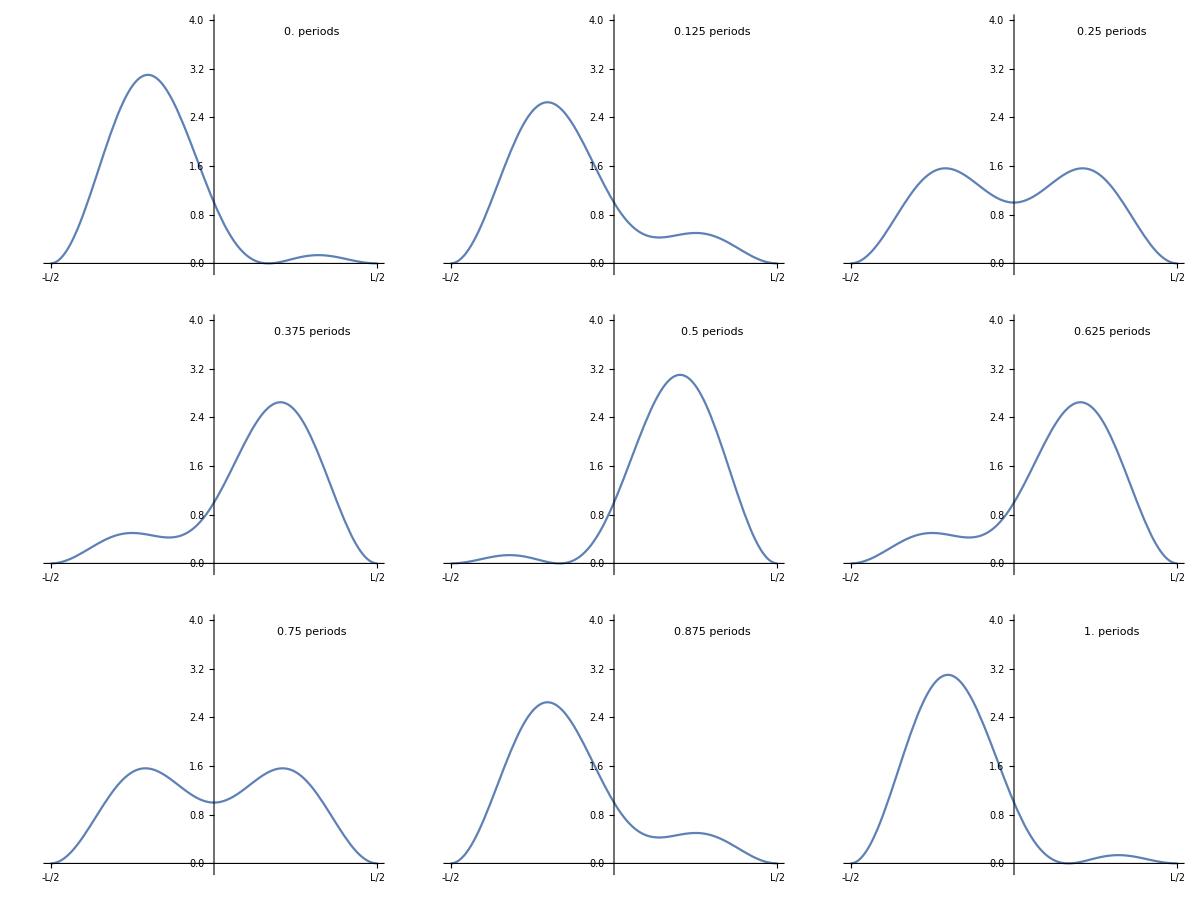

```mathematica
Grid[Partition[Table[Plot[ddPDF[ξ,τ],{ξ,-1/2,1/2},PlotRange->{-0.1,4},Ticks->{{{-1/2,-L/2},{1/2,L/2}},None},AxesLabel->{"",""},Epilog->{Style[Text[ToString[Round[τ,0.001]]<>" periods",{0.3,3.8}],FontSize->14]},ImageSize->300],{τ,0,1,1./8}],3]]
```

Time averaging by integrating over one period then dividing by time of integration:

```mathematica
timeAveragedPDF[ξ_]=Integrate[ddPDF[ξ,τ],{τ,0,1},Assumptions->ξ∈Reals]/1
```

Cos[π ξ]^2 (3-2 Cos[2 π ξ])

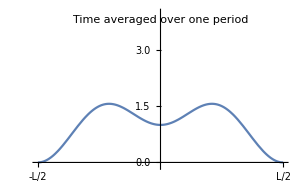

```mathematica
Plot[timeAveragedPDF[ξ],{ξ,-1/2,1/2},PlotRange->{-0.1,4},Ticks->{{{-1/2,-L/2},{1/2,L/2}},None},AxesLabel->{"",""},Epilog->{Style[Text["Time averaged over one period",{0,3.8}],FontSize->14]},ImageSize->300]
```

The symmetry of the stationary states returned!